# Optimality of Parseval frames on the sphere

The goal in this notebook is to perform the numerical experiments reported in “Frame theory on vector bundles,” by Samuel A. Ballas, Tom Needham, and Clayton Shonkwiler. This work was supported by the National Science Foundation (DMS–2107808 and DMS–2107700).

Specifically, the goal is to compare vector field reconstructions in the presence of measurement noise for Parseval frames and random frames on the 2-sphere.

First, we need to compute at a finite set of points, so we use Neil Sloane’s putatively optimal packing of 1592 points on the 2-sphere:

```mathematica
spherepoints=N[Normalize/@Partition[ToExpression[Import["http://neilsloane.com/packings/dim3/pack.3.1592.txt","Data"][[2;;]]],3]];
```

These are indeed nicely spread out on the sphere:

```mathematica
Graphics3D[{Sphere[],Black,Sphere[#,.015]&/@spherepoints}]
```

-Graphics3D-

Next, we need a way of generating smooth vector fields, which we will do using simplex noise. Simplex noise is related to Perlin noise, but involves interpolating between simplex vertices rather than cube vertices. Simplex noise has been ported to Python, and installing it is as simple as pip install opensimplex.

We can then use Python to generate vector fields using the following function:

```mathematica
simplex[pts_,seed_]:=ExternalEvaluate[{"Python","SessionProlog"->"import opensimplex"},"opensimplex.seed("<>ToString[seed]<>");a="<>StringReplace[ToString[pts],{"{"->"[","}"->"]"}]<>";[opensimplex.noise3(p[0],p[1],p[2]) for p in a]"];
```

So then we can generate smooth vector fields

```mathematica
vfs=Transpose/@ParallelTable[simplex[spherepoints,RandomInteger[{0,2^63}]],{1000},{3}];
```

And project them to the tangent space at each point:

```mathematica
tangentvfs=ParallelTable[vfs[[j,i]]-Projection[vfs[[j,i]],spherepoints[[i]]],{j,1,Length[vfs]},{i,1,Length[spherepoints]}];
```

This whole notebook uses a lot of memory, so it’s probably a good idea to store out data that takes time to generate in case we need to recover it after a crash:

```mathematica
Save[NotebookDirectory[]<>"tangentvfs.wl",tangentvfs]
```

Now, our Parseval frame is the orthogonal projection of the standard basis for ℝ^3 to the tangent space to each point on the sphere:

```mathematica
pframe=ParallelTable[IdentityMatrix[3]-Transpose[#].#&[{spherepoints[[i]]}],{i,1,Length[spherepoints]}];
```

Now for each vector field and at each point of the sphere we compute the dot products of the vector field at that point with the frame vectors at that point, add some small Gaussian white noise, then attempt to reconstruct the vector and record the squared error.

```mathematica
pframedata=ParallelTable[Block[{normals,frame,frameop,synthesis,analysis,basis},
frame=pframe[[i]];
basis=Transpose[NullSpace[{spherepoints[[i]]}]];
synthesis=Transpose[basis].Transpose[frame];
analysis=Transpose[synthesis].Transpose[basis].tangentvfs[[j,i]]+RandomVariate[MultinormalDistribution[.001 IdentityMatrix[3]]];
frameop=synthesis.Transpose[synthesis];
Norm[tangentvfs[[j,i]]-(basis.Inverse[frameop].synthesis.analysis)]^2],
{j,1,Length[tangentvfs]},{i,1,Length[spherepoints]}];
```

```mathematica
Save[NotebookDirectory[]<>"pframedata.wl",pframedata]
```

And we can compute the empirical CDF:

```mathematica
pd=EmpiricalDistribution[Mean/@pframedata];
```

Next, we build our random frames by generating 3 smooth random vector fields and normalizing at each point

```mathematica
frames=Map[Normalize,Map[Transpose,ParallelTable[simplex[spherepoints,RandomInteger[{0,2^63}]],{1000},{3},{3}],2],{3}];
```

…and then projecting to the tangent space at the point:

```mathematica
tframes=Table[frames[[k,i,j]]-Projection[frames[[k,i,j]],spherepoints[[i]]],{k,1,Length[frames]},{i,1,Length[spherepoints]},{j,1,3}];
```

```mathematica
Save[NotebookDirectory[]<>"tframes.wl",tframes]
```

Now we do the same noisy reconstruction experiment as before with each of the random frames:

```mathematica
tframedata=ParallelTable[Block[{normals,frame,frameop,synthesis,analysis,basis},
frame=tframes[[k,i]];
basis=Transpose[NullSpace[{spherepoints[[i]]}]];
synthesis=Transpose[basis].Transpose[frame];
analysis=Transpose[synthesis].Transpose[basis].tangentvfs[[j,i]]+RandomVariate[MultinormalDistribution[.001 IdentityMatrix[3]]];
frameop=synthesis.Transpose[synthesis];
Norm[tangentvfs[[j,i]]-(basis.Inverse[frameop].synthesis.analysis)]^2],
{k,1,Length[tframes]},{j,1,Length[tangentvfs]},{i,1,Length[spherepoints]}];
```

```mathematica
Save[NotebookDirectory[]<>"tframedata.wl",tframedata]
```

And now compute and save out the MSEs:

```mathematica
tframemeans=Table[Mean/@tframedata[[i]],{i,1,Length[tframes]}];
```

```mathematica
Save[NotebookDirectory[]<>"tframemeans.wl",tframemeans]
```

And the empirical CDFs:

```mathematica
td=Table[EmpiricalDistribution[tframemeans[[i]]],{i,1,Length[tframes]}];
```

We see that the MSEs for the Parseval frame lie in a small interval:

```mathematica
MinMax[Mean/@pframedata]
```

{0.00183429,0.00216157}

Whereas the MSEs of the random frames are all larger, and in some cases much, much larger:

```mathematica
MinMax[Flatten[Table[tframemeans[[i]],{i,1,Length[tframedata]}]]]
```

{0.00388179,51.3096}

For display purposes, we use the following color palette, which is Fabio Crameri's Batlow color map for categorical data:

```mathematica
cols={RGBColor[0.005193153367084745, 0.0982381170217676, 0.3498418809830899],RGBColor[0.9813535753006561, 0.8004061671470218, 0.9812666660455576],RGBColor[0.5112531863663102, 0.5108978758437912, 0.19329557161683117],RGBColor[0.13329781036453003, 0.3752817757604749, 0.3793954095265211],RGBColor[0.9506969673003716, 0.6166487438332956, 0.42862417218014814],RGBColor[0.06689896495473623, 0.26318767055475906, 0.37759435604864444],RGBColor[0.3023785627690957, 0.4502815737212346, 0.30012236213619936],RGBColor[0.7542682881292884, 0.5650332333700621, 0.211760789638594],RGBColor[0.9927709213388299, 0.7076892230192429, 0.7123800157834812],RGBColor[0.2090752388963242, 0.417412080725871, 0.3496767296453781],RGBColor[0.08835319612192202, 0.32216699518938113, 0.3847307176551048],RGBColor[0.8651682242450994, 0.5858818592158386, 0.30225470431144724],RGBColor[0.9885958122187206, 0.6613777963728396, 0.5752646372935034],RGBColor[0.4029676055462818, 0.48046597848254047, 0.24473116161388492],RGBColor[0.6315126979581867, 0.540752449196533, 0.17007475185076026],RGBColor[0.04937771055294349, 0.19107609466670547, 0.3658097737930779],RGBColor[0.9887543759571258, 0.753949469054436, 0.8466273512151431],RGBColor[0.4557739000068354, 0.4955846774693378, 0.2177743551480794],RGBColor[0.9127463125086187, 0.5991911996824932, 0.3609864487033381],RGBColor[0.07583316231246431, 0.29332080890607, 0.3819221265171391],RGBColor[0.25445231948078745, 0.43452908459242406, 0.32643417320075546],RGBColor[0.1068415417894461, 0.3497740690589232, 0.38454754507201544],RGBColor[0.3519760378874838, 0.46544005687368395, 0.27249229457065943],RGBColor[0.5700155866011719, 0.526185875241075, 0.17527272145547185],RGBColor[0.8116922177076217, 0.5751866844364272, 0.2525717360585131],RGBColor[0.03205278397327522, 0.14677416313591207, 0.3582388098645774],RGBColor[0.9758353864153829, 0.6380119755078629, 0.5018263821793786],RGBColor[0.1679516304435099, 0.3978894758325473, 0.36778403427924616],RGBColor[0.05916444726331392, 0.22984235549248522, 0.372251954677445],RGBColor[0.6937199105780304, 0.5537967644647263, 0.18261027740926],RGBColor[0.9911158331193111, 0.7304893697597771, 0.7786056353198485],RGBColor[0.9928132750814979, 0.6848154745222541, 0.6454230424726428],RGBColor[0.985503244682332, 0.7783778749992695, 0.9174441659006735],RGBColor[0.278171063633642, 0.44252433547295505, 0.3135517021145336],RGBColor[0.08155250132784678, 0.307858398947125, 0.38359755116259286],RGBColor[0.0199356188871784, 0.12298460990134438, 0.354119746868454],RGBColor[0.23136234768511588, 0.4261974566798758, 0.3385720498359743],RGBColor[0.8898997905034719, 0.5920866486650908, 0.3304540775020741],RGBColor[0.783415838135567, 0.570161596146816, 0.23096169818099238],RGBColor[0.6005204120803953, 0.5336045490746475, 0.1706478010371041],RGBColor[0.4290943832351661, 0.48801065150519185, 0.23109635675825485],RGBColor[0.14970605921174326, 0.3869750464356994, 0.37444878673936705],RGBColor[0.6626912095384206, 0.5475028509940739, 0.1740441636457403],RGBColor[0.9835737566710987, 0.6495902217676868, 0.5388187306681658],RGBColor[0.9914785301882021, 0.6731646593428352, 0.6108351051068914],RGBColor[0.5402253388010938, 0.5185841721042183, 0.183099222034565],RGBColor[0.9649427508668024, 0.6269343546666735, 0.4648597210220807],RGBColor[0.7243222900273982, 0.5596276419797932, 0.195408149901273],RGBColor[0.05472081902680487, 0.2112336395043889, 0.36918391837772296],RGBColor[0.37729103199175273, 0.47295177298973484, 0.25858753735262613],RGBColor[0.11899185226757944, 0.36284860147640574, 0.38271289196822167],RGBColor[0.06307118851928215, 0.2470851847296836, 0.3750497628325021],RGBColor[0.07111497011170888, 0.2784970788777719, 0.3798949405899265],RGBColor[0.18788592197876566, 0.4080032201407193, 0.35948448768180946],RGBColor[0.9931120849921747, 0.6963137745202373, 0.6791772587254299],RGBColor[0.48312282972791437, 0.5032161985929168, 0.2050370497105667],RGBColor[0.992054154948831, 0.7190487099910903, 0.7454025842160593],RGBColor[0.09661809539832363, 0.3361614658561598, 0.3851338100463711],RGBColor[0.042104481436739956, 0.16955702528601388, 0.3621513500244556],RGBColor[0.9331757063345633, 0.60736895111811, 0.39381661712976285],RGBColor[0.8389991521388886, 0.5803391491025478, 0.27635326813894934],RGBColor[0.9872798590258427, 0.7660469341106407, 0.8816985891558072],RGBColor[0.32700657046640985, 0.45790041408363436, 0.28637653338724006],RGBColor[0.9900183036533058, 0.7421024656402168, 0.8122852661755257],RGBColor[0.9833215511973703, 0.7909054211529133, 0.9537480969728521],RGBColor[0.04590454177718842, 0.18045998148098763, 0.36400713889938585],RGBColor[0.41596738524987337, 0.4842252855409939, 0.23789477741620474],RGBColor[0.6782435057902289, 0.5507118318166707, 0.1778028254107114],RGBColor[0.8777410037249749, 0.5888734340157754, 0.3160811744866095],RGBColor[0.9232998659240212, 0.6031373399712203, 0.3771387071173142],RGBColor[0.7689417224250781, 0.5676303553824138, 0.22104513938190246],RGBColor[0.942331841620567, 0.6118673492779588, 0.41100643836430095],RGBColor[0.2427949464944569, 0.43041813391463224, 0.3326345960882581],RGBColor[0.5851991583363613, 0.529926872028961, 0.17249347219852024],RGBColor[0.06493599599964549, 0.2552641171581149, 0.3763622349015682],RGBColor[0.05216442261319991, 0.2013231093466841, 0.36752442884120756],RGBColor[0.9864347952465548, 0.772184129460011, 0.8994929672526742],RGBColor[0.1586196382745385, 0.39253083557636365, 0.3713202601014282],RGBColor[0.6470984735516427, 0.544182954477616, 0.17146485486178015],RGBColor[0.9880460056954711, 0.7599636517823959, 0.8640778366211941],RGBColor[0.08477795683248569, 0.31504326897178137, 0.38423959035577426],RGBColor[0.10148075503464712, 0.3430356886142494, 0.3849805699006658],RGBColor[0.26624103559495926, 0.438555352552268, 0.32008520332780216],RGBColor[0.9916070333456365, 0.7247542962769521, 0.7619588693287709],RGBColor[0.33946912341713625, 0.4616845703169037, 0.27946782286049837],RGBColor[0.14125972272499474, 0.3812395532769262, 0.37713457767678255],RGBColor[0.07344021874372691, 0.2859415755335133, 0.38095684875304925],RGBColor[0.3900701662780218, 0.47671078250738447, 0.2516645567489511],RGBColor[0.314648370646325, 0.45410714049204104, 0.29327876318162127],RGBColor[0.06900153992680301, 0.2709216996688603, 0.37877419717350214],RGBColor[0.4970888484076958, 0.5070578325218741, 0.19899427513028659],RGBColor[0.057033202888293694, 0.22075440398869803, 0.3707499592314271],RGBColor[0.8522469835603281, 0.5830374368453031, 0.28903585603952037],RGBColor[0.012963349842328881, 0.11077922487868916, 0.3519924367491822],RGBColor[0.7976654656247937, 0.572681501867017, 0.24149026342353114],RGBColor[0.9923046658887763, 0.6790071219427478, 0.6282512775397422],RGBColor[0.1777520242325257, 0.4030413243185383, 0.36383253544698607],RGBColor[0.5256367015730944, 0.5147464059492216, 0.1879899267243815],RGBColor[0.8254723451653395, 0.5777251816245221, 0.26419650676207984],RGBColor[0.037449120197873095, 0.15831302906694084, 0.36021587390047566]};
```

And now we can plot the empirical CDFs:

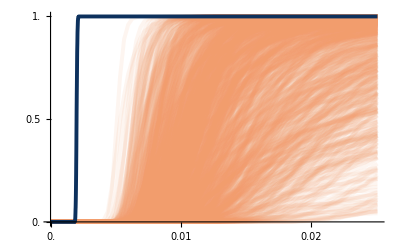

```mathematica
cdfs=Show[DiscretePlot[Evaluate@Table[CDF[td[[i]],x],{i,1,1000}],{x,0,40./1592,.5/1592},Joined->True,Filling->None,TicksStyle->"Label" ,PlotStyle->Directive[Opacity[.1],Thickness[.007],cols[[5]]],LabelStyle->Directive[FontFamily->"Latin Modern Math",14],Ticks->{Range[0,40./1592,.005],Range[0,1,.5]}],
DiscretePlot[CDF[pd,x],{x,0,40./1592,.01/1592},Joined->True,Filling->None,PlotStyle->Directive[Thickness[.007],cols[[16]]]]
]
```

```mathematica
Export[NotebookDirectory[]<>"cdfs.pdf",cdfs];
```

And the histograms of the MSEs for the Parseval frame and the best of the random frames:

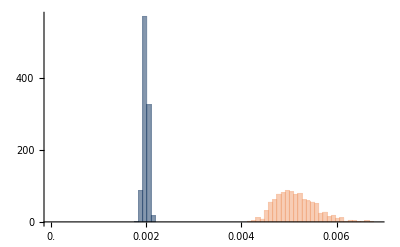

```mathematica
histocompare=With[{n=Position[Mean/@tframemeans,Min[Mean/@tframemeans]][[1,1]]},
Histogram[{Mean/@pframedata,Mean/@tframedata[[n]]},{0,11/1592,.14/1592},TicksStyle->"Label" ,ChartStyle->cols[[{16,5}]],LabelStyle->Directive[FontFamily->"Latin Modern Math",14],Ticks->{Range[0,.007,.001],Range[0,600,100]}]
]
```

```mathematica
Export[NotebookDirectory[]<>"histocompare.pdf",histocompare];
```